## Making polyominoes

```mathematica
R=10;p =5;
t=Flatten[Table[{i,j},{i,-5R,5R},{j,-5R,5R}],1];
t2=Select[t,0<=Abs[#[[1]]]^p+Abs[#[[2]]]^p≤(R)^p&];
dots[v_]:=Table[Disk[t2[[i]]+v,1/20],{i,1,Length[t2]}];
poliomino[v_]:=Table[Rectangle[v+t2[[i]]-{1/2,1/2},v+t2[[i]]+{1/2,1/2}],{i,1,Length[t2]}];
Graphics[{Red,EdgeForm[Thick],Opacity[0],poliomino[{0,0}],RGBColor[0,0,0.4],dots[{0,0}]}]
```

-Graphics-

```mathematica
Sqrt[15^{2}+6^{2}]//N
```

{16.1555}

```mathematica
Graphics[{Red,EdgeForm[Thick],Opacity[0],poliomino[{0,0}],RGBColor[0,0,0.4],dots[{0,0}]}]
```

-Graphics-

# Gambiarras

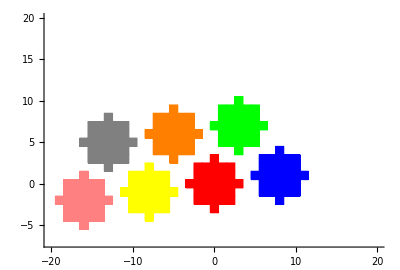

```mathematica
R= 3; p = 2;
t = Flatten[Table[{i, j}, {i, -5 R, 5 R}, {j, -5 R, 5 R}], 1];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Red, poliomino[{0, 0}]}];
A2 = Graphics[{EdgeForm[Thick], Green, poliomino[{3, 7}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Blue, poliomino[{8, 1}], RGBColor[0, 0, 0.4]}];
A4 = Graphics[{EdgeForm[Thick], Yellow, poliomino[{-8, -1}], RGBColor[0, 0, 0.4]}];
A5 = Graphics[{EdgeForm[Thick], Orange, poliomino[{-5, 6}], RGBColor[0, 0, 0.4]}];
A6 = Graphics[{EdgeForm[Thick], Pink, poliomino[{-16, -2}], RGBColor[0, 0, 0.4]}];
A7 = Graphics[{EdgeForm[Thick], Gray, poliomino[{-13, 5}], RGBColor[0, 0, 0.4]}];
v3 = {1, 0};
v3 = {1, 0};
v4 = {0, 0};
varMax = 20;
B = Show[A1, A2, A3, A4, A5, A6, A7, GridLines -> {Range[-20, 20], Range[-20, 20]}, PlotRange -> {{-20.1, 20}, {-7.1, 20}}, Axes -> True]
```

```mathematica
f[s_]=Log[2]/Log[s/(s-1)]
```

Log[2]/Log[s/(-1+s)]

```mathematica
Table[{s,f[s]}//N,{s,2,20}]
```

{{2.,1.},{3.,1.70951},{4.,2.40942},{5.,3.10628},{6.,3.80178},{7.,4.49656},{8.,5.19089},{9.,5.88495},{10.,6.57881},{11.,7.27254},{12.,7.96617},{13.,8.65972},{14.,9.35321},{15.,10.0466},{16.,10.7401},{17.,11.4334},{18.,12.1268},{19.,12.8201},{20.,13.5134}}

```mathematica
Exit[]
```

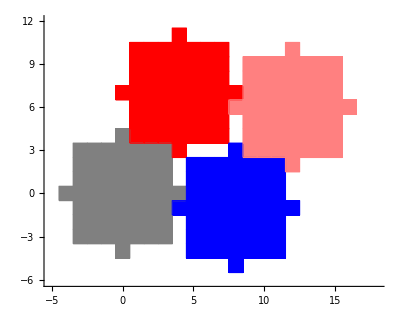

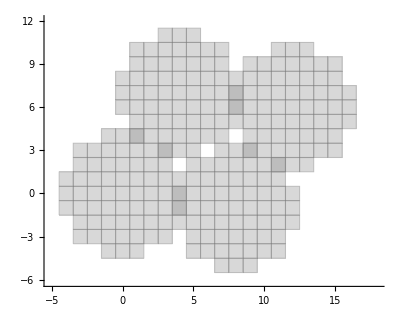

```mathematica
R= 4; p = 3;
t = Select[Flatten[Table[{i,j},{i,Floor[-R-1],Ceiling[R+1]},{j,Floor[-R-1],Ceiling[R+1]}],1],Abs[#[[1]]]^p+Abs[#[[2]]]^p≤R^p&];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Gray,poliomino[{0, 0}]}];
A2 = Graphics[{EdgeForm[Thick], Red, poliomino[{R, 2R-1}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Blue, poliomino[{2R, -1}], RGBColor[0, 0, 0.4]}];
A4= Graphics[{EdgeForm[Thick], Pink, poliomino[{3R, 2R-2}], RGBColor[0, 0, 0.4]}];
B = Show[A1, A2, A3,A4, GridLines -> {Range[-20, 40], Range[-20, 40]}, PlotRange -> {{-5.1, 18}, {-6.1, 12}}, Axes -> True]

R1= (1+4^3)^(1/3) ; p = 3;
t = Select[Flatten[Table[{i,j},{i,Floor[-R1-1],Ceiling[R1+1]},{j,Floor[-R1-1],Ceiling[R1+1]}],1],Abs[#[[1]]]^p+Abs[#[[2]]]^p≤R1^p&];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R1)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Gray,Opacity[0.3], poliomino[{0, 0}]}];
A2 = Graphics[{EdgeForm[Thick], Gray,Opacity[0.3], poliomino[{R, 2R-1}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Gray,Opacity[0.3], poliomino[{2R, -1}], RGBColor[0, 0, 0.4]}];
A4= Graphics[{EdgeForm[Thick], Gray,Opacity[0.3], poliomino[{3R, 2R-2}], RGBColor[0, 0, 0.4]}];
B = Show[A1, A2, A3,A4, GridLines -> {Range[-20, 40], Range[-20, 40]}, PlotRange -> {{-5.1, 18}, {-6.1, 12}}, Axes -> True]
```

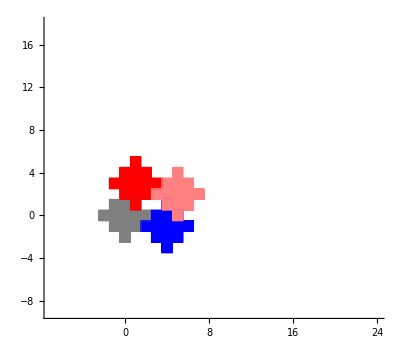

```mathematica
R= 2; p = 1;
t = Select[Flatten[Table[{i,j},{i,Floor[-R-1],Ceiling[R+1]},{j,Floor[-R-1],Ceiling[R+1]}],1],Abs[#[[1]]]^p+Abs[#[[2]]]^p≤R^p&];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Gray,poliomino[{0, 0}]}];
A2 = Graphics[{EdgeForm[Thick], Red, poliomino[{R-1, 2R-1}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Blue, poliomino[{2R, -1}], RGBColor[0, 0, 0.4]}];
A4= Graphics[{EdgeForm[Thick], Pink, poliomino[{3R-1, 2R-2}], RGBColor[0, 0, 0.4]}];
B = Show[A1, A2, A3,A4, GridLines -> {Range[-20, 40], Range[-20, 40]}, PlotRange -> {{-7.1, 24}, {-9.1, 18}}, Axes -> True]
```

```mathematica
11^2
```

121

```mathematica
4*36-6-1
```

```mathematica
121/137.
```

0.883212

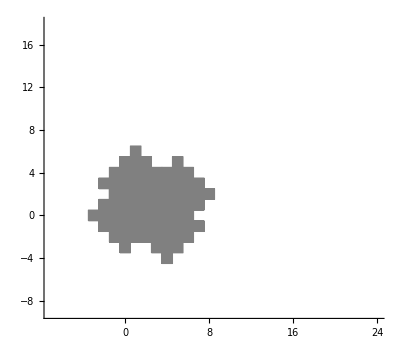

```mathematica
R1= (1+R^p)^(1/p) ; 
t = Select[Flatten[Table[{i,j},{i,Floor[-R1-1],Ceiling[R1+1]},{j,Floor[-R1-1],Ceiling[R1+1]}],1],Abs[#[[1]]]^p+Abs[#[[2]]]^p≤R1^p&];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R1)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Gray,poliomino[{0, 0}]}];
A2 = Graphics[{EdgeForm[Thick], Gray, poliomino[{R-1, 2R-1}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Gray, poliomino[{2R, -1}], RGBColor[0, 0, 0.4]}];
A4= Graphics[{EdgeForm[Thick], Gray, poliomino[{3R-1, 2R-2}], RGBColor[0, 0, 0.4]}];
B = Show[A1, A2, A3,A4, GridLines -> {Range[-20, 40], Range[-20, 40]}, PlotRange -> {{-7.1, 24}, {-9.1, 18}}, Axes -> True]
```

```mathematica
Exit[]
```

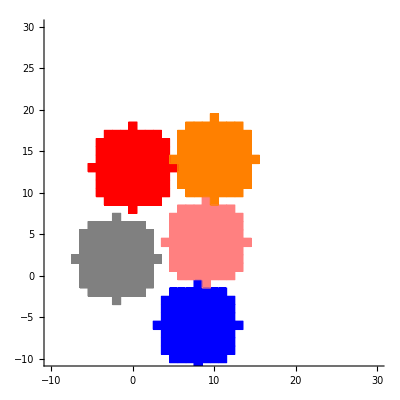

```mathematica
R= 5; p = 3;
t = Select[Flatten[Table[{i,j},{i,Floor[-R-1],Ceiling[R+1]},{j,Floor[-R-1],Ceiling[R+1]}],1],Abs[#[[1]]]^p+Abs[#[[2]]]^p≤R^p&];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Gray,poliomino[{-2, 2}]}];
A2 = Graphics[{EdgeForm[Thick], Red, poliomino[{R-5, 2R+3}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Blue, poliomino[{R+3, -2R+4}], RGBColor[0, 0, 0.4]}];
A4 = Graphics[{EdgeForm[Thick], Pink, poliomino[{2R-1, R-1}], RGBColor[0, 0, 0.4]}];
A5 = Graphics[{EdgeForm[Thick], Orange, poliomino[{2R, 2R+4}], RGBColor[0, 0, 0.4]}];
B = Show[A1, A2, A3,A4,A5, GridLines -> {Range[-20, 40], Range[-20, 40]}, PlotRange -> {{-10.1, 30}, {-10.1, 30}}, Axes -> True]
```

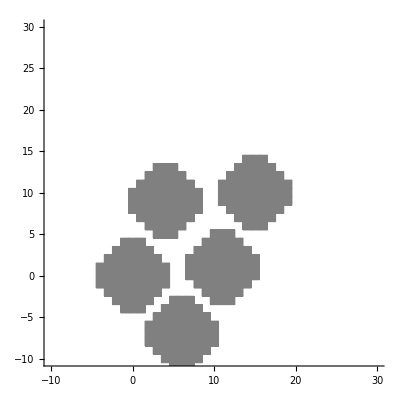

```mathematica
R1= (1+4^2)^(1/2) ; p = 2;
t = Select[Flatten[Table[{i,j},{i,Floor[-R1-1],Ceiling[R1+1]},{j,Floor[-R1-1],Ceiling[R1+1]}],1],Abs[#[[1]]]^p+Abs[#[[2]]]^p≤R1^p&];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R1)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Gray,poliomino[{0, 0}]}];
A2 = Graphics[{EdgeForm[Thick], Gray, poliomino[{R-1, 2R-1}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Gray, poliomino[{R+1, -R-2}], RGBColor[0, 0, 0.4]}];
A4 = Graphics[{EdgeForm[Thick], Gray, poliomino[{2R+1, 1}], RGBColor[0, 0, 0.4]}];
A5 = Graphics[{EdgeForm[Thick], Gray, poliomino[{3R, 2R}], RGBColor[0, 0, 0.4]}];
B = Show[A1, A2, A3,A4,A5, GridLines -> {Range[-20, 40], Range[-20, 40]}, PlotRange -> {{-10.1, 30}, {-10.1, 30}}, Axes -> True]
```

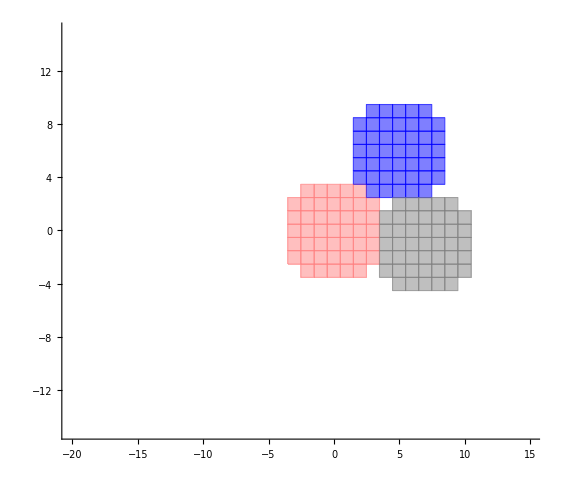

```mathematica
R=√13;p =3;
t=Flatten[Table[{i,j},{i,-5R,5R},{j,-5R,5R}],1];
t2=Select[t,0<=Abs[#[[1]]]^p+Abs[#[[2]]]^p≤(R)^p&];
dots[v_]:=Table[Disk[t2[[i]]+v,1/20],{i,1,Length[t2]}];
poliomino[v_]:=Table[Rectangle[v+t2[[i]]-{1/2,1/2},v+t2[[i]]+{1/2,1/2}],{i,1,Length[t2]}];
A1=Graphics[{EdgeForm[Thick],Pink,Opacity[0.5],poliomino[{0,0}]}];
A2=Graphics[{EdgeForm[Thick],Blue,Opacity[0.5],poliomino[{5,6}]}];
A3=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5],poliomino[{7,-1}]}];
A4=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5],poliomino[{-8,1}]}];
A5=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5], poliomino[{-2,7}]}];
A6=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5],poliomino[{-16,2}]}];
A7=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5],poliomino[{-12,9}]}];
A9=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5],poliomino[{4,-8}]}];
A10=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5],poliomino[{-4,-6}]}];
A11=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5],poliomino[{8,-1}]}];
A12=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5],poliomino[{-8,2}]}];
A13=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5], poliomino[{-4,8}]}];
A14=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5],poliomino[{-16,2}]}];
A15=Graphics[{EdgeForm[Thick],Gray,Opacity[0.5],poliomino[{-12,9}]}];
v3={1, 0};
v3={1, 0};
v4={0,0};
varMax=20;
B=Show[A1,A2,A3,GridLines->{Range[-20,20],Range[-20,20]},PlotRange->{{-20.1,15},{-15.1,15}},Axes-> True]
```

```mathematica
{4.3}^{4}//N
```

{341.88}

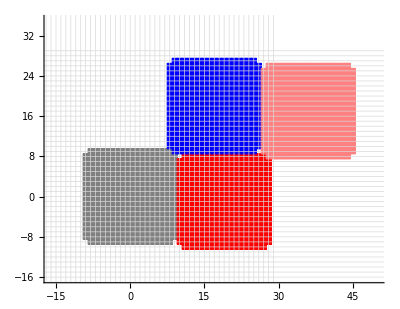

```mathematica
R= 9.3; p = 10;
t = Select[Flatten[Table[{i,j},{i,Floor[-R-1],Ceiling[R+1]},{j,Floor[-R-1],Ceiling[R+1]}],1],Abs[#[[1]]]^p+Abs[#[[2]]]^p≤R^p&];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Gray,poliomino[{0, 0}]}];
A2 = Graphics[{EdgeForm[Thick], Red, poliomino[{2 Floor[R]+1, -1}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Blue, poliomino[{2Floor[R]-1, 2Floor[R]}], RGBColor[0, 0, 0.4]}];
A4 = Graphics[{EdgeForm[Thick], Pink, poliomino[{4Floor[R], 2Floor[R]-1}], RGBColor[0, 0, 0.4]}];
A5 = Graphics[{EdgeForm[Thick], Orange, poliomino[{5Floor[R]-2, -3}], RGBColor[0, 0, 0.4]}];
B = Show[A1, A2, A3,A4, GridLines -> {Range[-20, 50], Range[-20, 40]}, PlotRange -> {{-16.1, 50}, {-16.1, 35}}, Axes -> True]
```

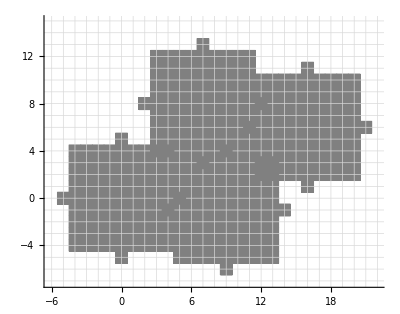

```mathematica
R1= 5 ; ;
t = Select[Flatten[Table[{i,j},{i,Floor[-R1-1],Ceiling[R1+1]},{j,Floor[-R1-1],Ceiling[R1+1]}],1],Abs[#[[1]]]^p+Abs[#[[2]]]^p≤R1^p&];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R1)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Gray,poliomino[{0, 0}]}];
A2 = Graphics[{EdgeForm[Thick], Gray, poliomino[{2 Floor[R]+1, -1}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Gray, poliomino[{2Floor[R]-1, 2Floor[R]}], RGBColor[0, 0, 0.4]}];
A4 = Graphics[{EdgeForm[Thick], Gray, poliomino[{4Floor[R], Floor[R]+2}], RGBColor[0, 0, 0.4]}];
A5 = Graphics[{EdgeForm[Thick], Gray, poliomino[{5Floor[R]-2, -3}], RGBColor[0, 0, 0.4]}];
 Show[A1, A2, A3,A4, GridLines -> {Range[-20, 40], Range[-20, 21]}, PlotRange -> {{-6.1, 22}, {-7.1, 15}}, Axes -> True]
```

```mathematica
R1//N
```

5.15467

```mathematica
(3^p+(Floor[R]+1)^p)^(1/p) ;
```

```mathematica
4*36+4*6-1
```

167

```mathematica
77/79//N
```

0.974684

10

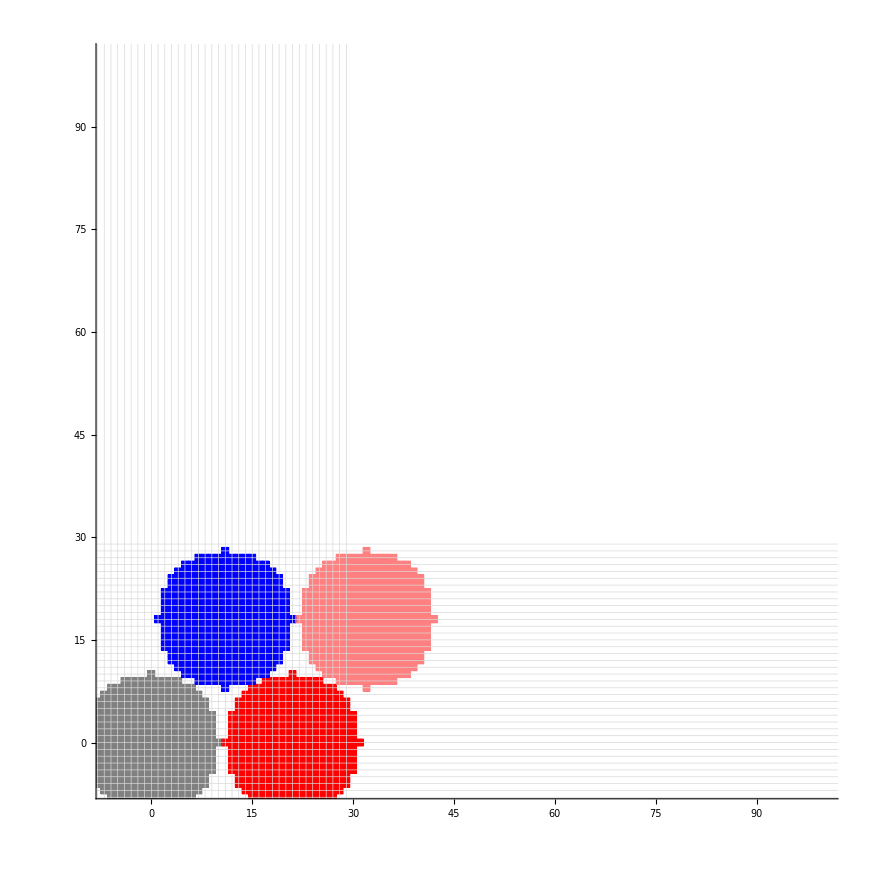

```mathematica
R= 10
.2; p = 2;
t = Select[Flatten[Table[{i,j},{i,Floor[-R-1],Ceiling[R+1]},{j,Floor[-R-1],Ceiling[R+1]}],1],Abs[#[[1]]]^p+Abs[#[[2]]]^p≤R^p&];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Gray,poliomino[{0, 0}]}];
A2 = Graphics[{EdgeForm[Thick], Red, poliomino[{2 Floor[R]+1,0}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Blue, poliomino[{Floor[R]+1, 2Floor[R]-Floor[R/4]}], RGBColor[0, 0, 0.4]}];
A4 = Graphics[{EdgeForm[Thick], Pink, poliomino[{3Floor[R] +2,2Floor[R]-Floor[R/4]}], RGBColor[0, 0, 0.4]}];
A5 = Graphics[{EdgeForm[Thick], Green, poliomino[{3Floor[R]+5, -2}], RGBColor[0, 0, 0.4]}];
B = Show[A1, A2, A3,A4, GridLines -> {Range[-20, 50], Range[-20, 40]}, PlotRange -> {{-6.1, 100}, {-6.1, 100}}, Axes -> True]
```

```mathematica
Det[{{2s+1,-2},{2s-2,2s-1}}]
```

-5+4 s+4 s^2

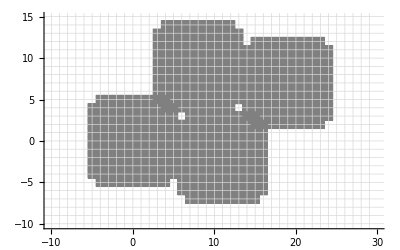

```mathematica
R1= 5.5  ;
t = Select[Flatten[Table[{i,j},{i,Floor[-R1-1],Ceiling[R1+1]},{j,Floor[-R1-1],Ceiling[R1+1]}],1],Abs[#[[1]]]^p+Abs[#[[2]]]^p≤R1^p&];
t2 = Select[t, 0 <= Abs[#[[1]]]^p + Abs[#[[2]]]^p <= (R1)^p &];
dots[v_] := Table[Disk[t2[[i]] + v, 1/20], {i, 1, Length[t2]}];
poliomino[v_] := Table[Rectangle[v + t2[[i]] - {1/2, 1/2}, v + t2[[i]] + {1/2, 1/2}], {i, 1, Length[t2]}];
A1 = Graphics[{EdgeForm[Thick], Gray,poliomino[{0, 0}]}];
A2 = Graphics[{EdgeForm[Thick], Gray, poliomino[{2 Floor[R]+1,-2}], RGBColor[0, 0, 0.4]}];
A3 = Graphics[{EdgeForm[Thick], Gray, poliomino[{2Floor[R]-2, 2Floor[R]-1}], RGBColor[0, 0, 0.4]}];
A4 = Graphics[{EdgeForm[Thick], Gray, poliomino[{4Floor[R] -1,2Floor[R]-3}], RGBColor[0, 0, 0.4]}];
A5 = Graphics[{EdgeForm[Thick], Gray, poliomino[{3Floor[R]+5, -2}], RGBColor[0, 0, 0.4]}];
B = Show[A1, A2, A3,A4, GridLines -> {Range[-20, 50], Range[-20, 40]}, PlotRange -> {{-10.1, 30}, {-10.1, 15}}, Axes -> True]
```